```mathematica
rounds={
{{{1,5},{7,8}},{{2,3},{4,6}}},
{{{4,7},{6,8}},{{1,2},{3,5}}},
{{{3,4},{5,7}},{{2,6},{1,8}}},
{{{1,6},{4,5}},{{3,7},{2,8}}},
{{{5,6},{2,7}},{{1,4},{3,8}}},
{{{4,8},{2,5}},{{6,7},{1,3}}},
{{{1,7},{2,4}},{{3,6},{5,8}}}
}
```

{{{{1,5},{7,8}},{{2,3},{4,6}}},{{{4,7},{6,8}},{{1,2},{3,5}}},{{{3,4},{5,7}},{{2,6},{1,8}}},{{{1,6},{4,5}},{{3,7},{2,8}}},{{{5,6},{2,7}},{{1,4},{3,8}}},{{{4,8},{2,5}},{{6,7},{1,3}}},{{{1,7},{2,4}},{{3,6},{5,8}}}}

```mathematica
met=Table[
Table[
Table[UndirectedEdge[team[[1]],team[[2]],"met"],{team,match}
],
{match,round}
]
,{round,rounds}
]//Flatten
```

{15met,78met,23met,46met,47met,68met,12met,35met,34met,57met,26met,18met,16met,45met,37met,28met,56met,27met,14met,38met,48met,25met,67met,13met,17met,24met,36met,58met}

```mathematica
Graph[met]//AdjacencyMatrix//MatrixForm
```

(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)

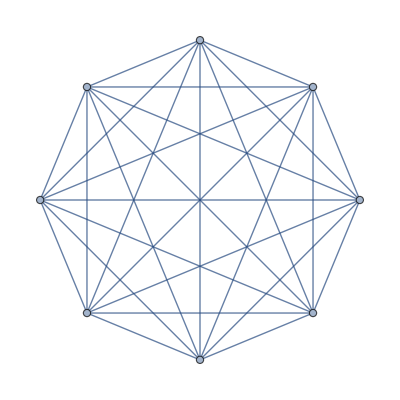

```mathematica
Graph[met]
```

```mathematica
tegen=Table[
Table[
With[{team1=match[[1]],team2=match[[2]]},
{
UndirectedEdge[team1[[1]],team2[[1]],"tegen"],
UndirectedEdge[team1[[1]],team2[[2]],"tegen"],
UndirectedEdge[team1[[2]],team2[[1]],"tegen"],
UndirectedEdge[team1[[2]],team2[[2]],"tegen"]
}
],
{match,round}
]
,{round,rounds}
]//Flatten
```

{17tegen,18tegen,57tegen,58tegen,24tegen,26tegen,34tegen,36tegen,46tegen,48tegen,76tegen,78tegen,13tegen,15tegen,23tegen,25tegen,35tegen,37tegen,45tegen,47tegen,21tegen,28tegen,61tegen,68tegen,14tegen,15tegen,64tegen,65tegen,32tegen,38tegen,72tegen,78tegen,52tegen,57tegen,62tegen,67tegen,13tegen,18tegen,43tegen,48tegen,42tegen,45tegen,82tegen,85tegen,61tegen,63tegen,71tegen,73tegen,12tegen,14tegen,72tegen,74tegen,35tegen,38tegen,65tegen,68tegen}

```mathematica
Graph[tegen]//AdjacencyMatrix//MatrixForm
```

(0 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 0 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 0 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 0 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 0 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 0 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 0 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 0)

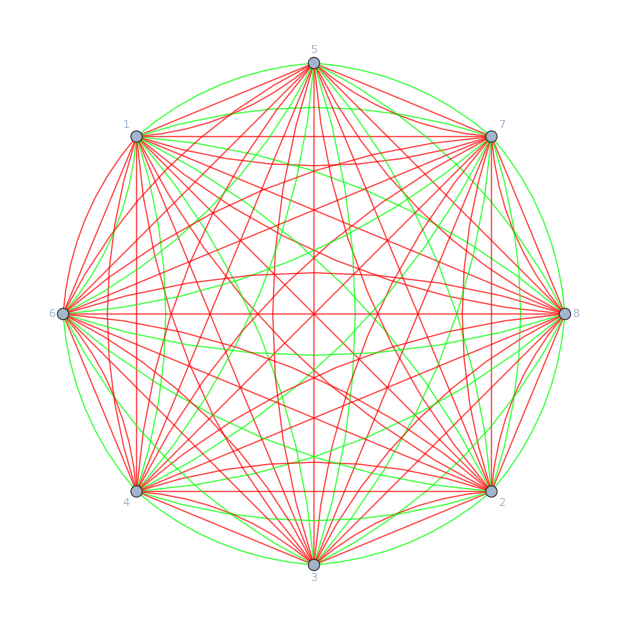

```mathematica
Graph[Join[met,tegen],VertexLabels->"Name",EdgeStyle->Join[Map[#->Green&,met],Map[#->Red&,tegen]], GraphLayout->"CircularEmbedding"]
```

```mathematica
rounds={
{{{1,5},{7,8}},{{2,3},{4,6}}},
{{{4,7},{6,8}},{{1,2},{3,5}}},
{{{3,4},{5,7}},{{2,6},{1,8}}},
{{{1,6},{4,5}},{{3,7},{2,8}}},
{{{5,6},{2,7}},{{1,4},{3,8}}},
{{{4,8},{2,5}},{{6,7},{1,3}}},
{{{1,7},{2,4}},{{3,6},{5,8}}}
}
```

```mathematica
TableForm[
With[{name=RandomSample[{"Eddy","Polle","Pool","Josje","Kloenie","Gerrit","Cox","Lode"}]},
Table[
Table[
With[{team1=match[[1]],team2=match[[2]]},
StringPadLeft[name[[team1[[1]]]],8]<> " MET "<> StringPadRight[name[[team1[[2]]]],8]<>" TEGEN "<>StringPadLeft[name[[team2[[1]]]],8]<> " MET "<> StringPadRight[name[[team2[[2]]]],8]
],
{match,round}
]
,{round,{
{{{1,5},{7,8}},{{2,3},{4,6}}},
{{{4,7},{6,8}},{{1,2},{3,5}}},
{{{3,4},{5,7}},{{2,6},{1,8}}},
{{{1,6},{4,5}},{{3,7},{2,8}}},
{{{5,6},{2,7}},{{1,4},{3,8}}},
{{{4,8},{2,5}},{{6,7},{1,3}}},
{{{1,7},{2,4}},{{3,6},{5,8}}}
}}
]
],
TableHeadings->{{Dag1EersteMatch,Dag1TweedeMatch,Dag1DerdeMatch,Dag2EersteMatch,Dag2TweedeMatch,Dag2DerdeMatch,Dag3EersteMatch}, {Terrein1,Terrein2}},
TableAlignments->Center
]
```

| Terrein1 | Terrein2
Dag1EersteMatch |     Eddy MET Gerrit   TEGEN    Josje MET Cox      |     Lode MET Pool     TEGEN    Polle MET Kloenie 
Dag1TweedeMatch |    Polle MET Josje    TEGEN  Kloenie MET Cox      |     Eddy MET Lode     TEGEN     Pool MET Gerrit  
Dag1DerdeMatch |     Pool MET Polle    TEGEN   Gerrit MET Josje    |     Lode MET Kloenie  TEGEN     Eddy MET Cox     
Dag2EersteMatch |     Eddy MET Kloenie  TEGEN    Polle MET Gerrit   |     Pool MET Josje    TEGEN     Lode MET Cox     
Dag2TweedeMatch |   Gerrit MET Kloenie  TEGEN     Lode MET Josje    |     Eddy MET Polle    TEGEN     Pool MET Cox     
Dag2DerdeMatch |    Polle MET Cox      TEGEN     Lode MET Gerrit   |  Kloenie MET Josje    TEGEN     Eddy MET Pool    
Dag3EersteMatch |     Eddy MET Josje    TEGEN     Lode MET Polle    |     Pool MET Kloenie  TEGEN   Gerrit MET Cox